```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
bottomx=Import["bottom_displacement_x.txt","Table"];
bottomy=Import["bottom_displacement_y.txt","Table"];
topx=Import["top_displacement_x.txt","Table"];
topy=Import["top_displacement_y.txt","Table"];
```

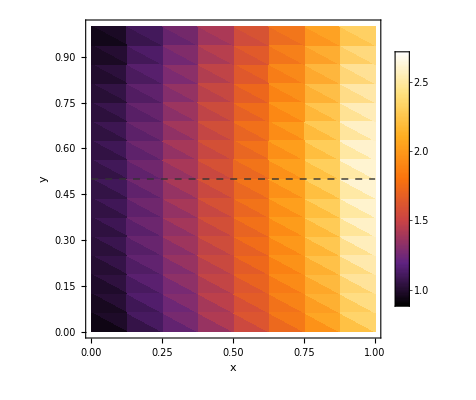

x12.pdf

```mathematica
allDatax=Join[bottomx,topx];
plotx=ListDensityPlot[allDatax,Mesh->None,ColorFunction->"SunsetColors",Frame->True,Axes->False,FrameLabel->{"x","y"},PlotLegends->Automatic,PlotRange->All,Epilog->{{Dashed,GrayLevel[0.2],AbsoluteThickness[1],Line[{{0,0.5},{1,0.5}}]}}]
Export["x12.pdf", plotx]
```

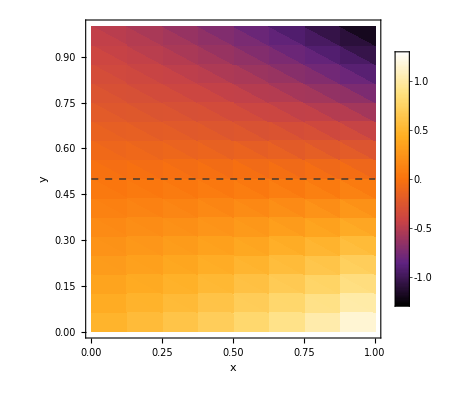

y12.pdf

```mathematica
allDatay=Join[bottomy,topy];
ploty=ListDensityPlot[allDatay,Mesh->None,ColorFunction->"SunsetColors",Frame->True,Axes->False,FrameLabel->{"x","y"},PlotLegends->Automatic,PlotRange->All,Epilog->{{Dashed,GrayLevel[0.2],AbsoluteThickness[1],Line[{{0,0.5},{1,0.5}}]}}]
Export["y12.pdf", ploty]
```

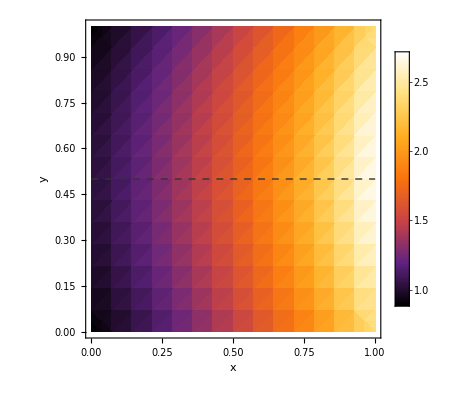

exactx.pdf

```mathematica
ux[x_,y_]:=Exp[x]Cos[y - 0.5]; 
exactx=DensityPlot[ux[x,y],{x,0,1},{y,0,1},Mesh->None,ColorFunction->"SunsetColors",Frame->True,Axes->False,FrameLabel->{"x","y"},PlotLegends->Automatic,PlotRange->All,Epilog->{{Dashed,GrayLevel[0.2],AbsoluteThickness[1],Line[{{0,0.5},{1,0.5}}]}}]
Export["exactx.pdf", exactx]
```

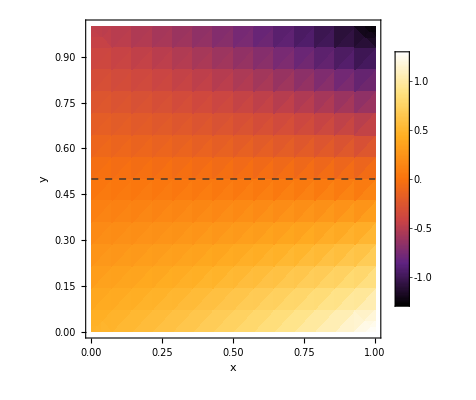

exacty.pdf

```mathematica
uy[x_,y_]:=-Exp[x]Sin[y - 0.5]; 
exacty=DensityPlot[uy[x,y],{x,0,1},{y,0,1},Mesh->None,ColorFunction->"SunsetColors",Frame->True,Axes->False,FrameLabel->{"x","y"},PlotLegends->Automatic,PlotRange->All,Epilog->{{Dashed,GrayLevel[0.2],AbsoluteThickness[1],Line[{{0,0.5},{1,0.5}}]}}]
Export["exacty.pdf", exacty]
```